### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[733448814971]
```

<|Index→733448814971,QCode→32342434232423224,RuleSet→{AA→AB,BB→AA,B→AA,A→B}|>

We can pull out the ruleset itself:

```mathematica
rs[["RuleSet"]]
```

{AA→AB,BB→AA,B→AA,A→B}

We generate the sessie and its causal network, again giving it a convenient name:


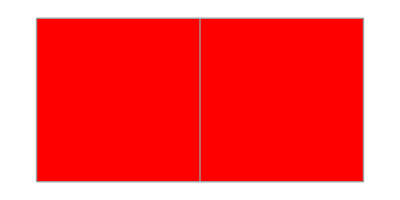

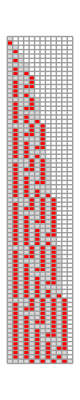
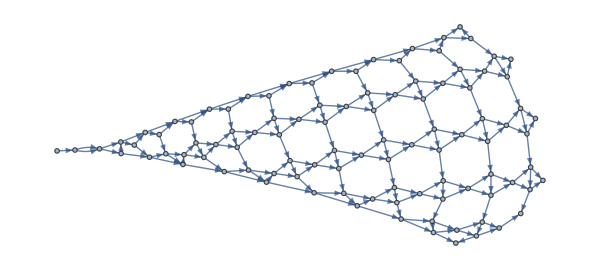
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "A",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,2→3,2→3,3→4,3→5,4→5,5→6,5→7,6→7,6→8,4→8,«752»,363→395,394→396,395→396,395→397,366→397,397→398,366→398,397→399,398→399,398→400,369→400}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1},{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{},{1,2},{},{1,2},{1,2},{},{1,2},{1,2},{},{1,2},{1,2}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,31]
```

{{292,2},{323,2},{325,1},{328,2},{331,2},{334,2},{337,2},{340,2},{343,2},{346,2},{349,2},{352,2},{355,2},{360,1},{363,1},{366,1},{369,1}}

```mathematica
nds[[1;;366]]
```

{{1},{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,34},{30,31},{1,2},{32,33},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32},{1,2},{1,2},{31,32}}

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;366]]]
```

{{1},{1,1},€_(n$1⊨1)^2[{1,2+2 (-1+n$1)}],€^2[{1,2}],€_(n$1⊨1)^2[{1+n$1,2+n$1}],{1,2},{4,5},€_(n$3⊨1)^2[€_(n$1⊨1)^2[{1,6-4 n$1-9 n$3+9 n$1 n$3}],€_(n$2⊨1)^2[{-9+3 n$2+9 n$3,-8+3 n$2+9 n$3},{1,2},{-6+2 n$2+9 n$3,-5+2 n$2+9 n$3},€^(-2+3 n$3)[€^2[{1,2}],{-7+2 n$2+9 n$3,-6+2 n$2+9 n$3}]],€_(n$1⊨1)^2[{1,3-n$1+9 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-6+3 n$2+9 n$3,-5+3 n$2+9 n$3},{1,2},{-3+2 n$2+9 n$3,-2+2 n$2+9 n$3},€^(-1+3 n$3)[€^2[{1,2}],{-4+2 n$2+9 n$3,-3+2 n$2+9 n$3}]],€_(n$1⊨1)^2[{1,2 n$1+9 (-1+n$1) n$3}],€_(n$2⊨1)^2[{-3+3 n$2+9 n$3,-2+3 n$2+9 n$3},{1,2},{2 n$2+9 n$3,1+2 n$2+9 n$3},€^(3 n$3)[€^2[{1,2}],{-1+2 n$2+9 n$3,2 n$2+9 n$3}]]],€_(n$1⊨1)^2[{1,-3+18 (-1+n$1)+5 n$1}],€_(n$2⊨1)^2[{21+3 (-1+n$2),22+3 (-1+n$2)},{1,2},{23+2 (-1+n$2),24+2 (-1+n$2)},€^7[€^2[{1,2}],{22+2 (-1+n$2),23+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+26 (-1+n$1)}],€_(n$2⊨1)^2[{24+3 (-1+n$2),25+3 (-1+n$2)},{1,2},{26+2 (-1+n$2),27+2 (-1+n$2)},€^8[€^2[{1,2}],{25+2 (-1+n$2),26+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+29 (-1+n$1)}],€_(n$2⊨1)^2[{27+3 (-1+n$2),28+3 (-1+n$2)},{1,2},{29+2 (-1+n$2),30+2 (-1+n$2)},€^9[€^2[{1,2}],{28+2 (-1+n$2),29+2 (-1+n$2)}]],€_(n$1⊨1)^2[{1,2+32 (-1+n$1)}],{30,31},{1,2},{32,33},€^3[€^2[{1,2}],{31,32}]}

The most compressed part is

```mathematica
{ExpandAll[%]}
```

{{{1},{1,1},{1,2},{1,4},{1,2},{1,2},{2,3},{3,4},{1,2},{4,5},{1,2},{1,7},{3,4},{1,2},{5,6},{1,2},{1,2},{4,5},{6,7},{1,2},{7,8},{1,2},{1,2},{6,7},{1,2},{1,10},{6,7},{1,2},{8,9},{1,2},{1,2},{7,8},{1,2},{1,2},{7,8},{9,10},{1,2},{10,11},{1,2},{1,2},{9,10},{1,2},{1,2},{9,10},{1,2},{1,13},{9,10},{1,2},{11,12},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{1,2},{1,2},{10,11},{12,13},{1,2},{13,14},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,2},{12,13},{1,2},{1,16},{12,13},{1,2},{14,15},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{1,2},{1,2},{13,14},{15,16},{1,2},{16,17},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,2},{15,16},{1,2},{1,19},{15,16},{1,2},{17,18},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{1,2},{1,2},{16,17},{18,19},{1,2},{19,20},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,2},{18,19},{1,2},{1,22},{18,19},{1,2},{20,21},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{1,2},{1,2},{19,20},{21,22},{1,2},{22,23},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,2},{21,22},{1,2},{1,25},{21,22},{1,2},{23,24},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{1,2},{1,2},{22,23},{24,25},{1,2},{25,26},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,2},{24,25},{1,2},{1,28},{24,25},{1,2},{26,27},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{1,2},{1,2},{25,26},{27,28},{1,2},{28,29},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,2},{27,28},{1,2},{1,31},{27,28},{1,2},{29,30},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{1,2},{1,2},{28,29},{30,31},{1,2},{31,32},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31},{1,2},{1,2},{30,31}}}

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```